# practical 3 (secant method) ques 1

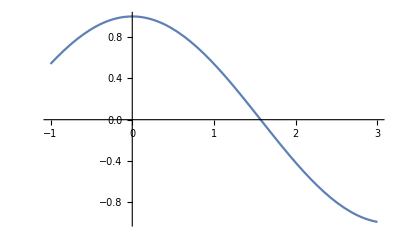

```mathematica
f[x_]=Cos[x];
Plot[f[x],{x,-1,3}]
```

```mathematica
x0=1;
x1=2;
Nmax=20;
eps=10^(-6);
Print["f[x]=",f[x]];
For[i=1,i≤Nmax,i++,
x2=N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2];
Print["In",i,"th Number of iterations the root is :",x2];
Print["estimated error is :",Abs[x1-x0]]];
Print["root is :",x2];
Print["estimated error is:",Abs[x2-x1]];
```

f[x]=Cos[x]

In1th Number of iterations the root is :1.5649

estimated error is :0.435096

In2th Number of iterations the root is :1.57098

estimated error is :0.0060742

In3th Number of iterations the root is :1.5708

estimated error is :0.000182249

Return[1.5708]

root is :1.5708

estimated error is:1.02185×10^-9

```mathematica
ques 2
```

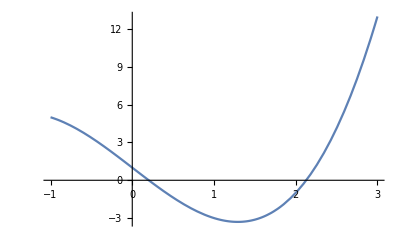

```mathematica
f[x_]= x^3-5*x+1;
Plot[f[x],{x,-1,3}]
```

```mathematica
x0=0;
x1=1;
Nmax=20;
eps=10^(-6);
Print["f[x]=",f[x]];
For[i=1,i≤Nmax,i++,
x2=N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2];
Print["In",i,"th Number of iterations the root is :",x2];
Print["estimated error is :",Abs[x1-x0]]];
Print["root is :",x2];
Print["estimated error is:",Abs[x2-x1]];
```

f[x]=1-5 x+x^3

In1th Number of iterations the root is :0.25

estimated error is :0.75

In2th Number of iterations the root is :0.186441

estimated error is :0.0635593

In3th Number of iterations the root is :0.201736

estimated error is :0.0152956

In4th Number of iterations the root is :0.20164

estimated error is :0.0000964033

Return[0.20164]

root is :0.20164

estimated error is:1.7717×10^-7

# ques 3

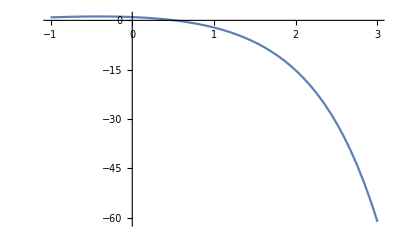

```mathematica
f[x_]=  Cos[x]-x*Exp[x];
Plot[f[x],{x,-1,3}]
```

```mathematica
x0=0;
x1=1;
Nmax=20;
eps=10^(-6);
Print["f[x]=",f[x]];
For[i=1,i≤Nmax,i++,
x2=N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2];
Print["In",i,"th Number of iterations the root is :",x2];
Print["estimated error is :",Abs[x1-x0]]];
Print["root is :",x2];
Print["estimated error is:",Abs[x2-x1]];
```

f[x]=-ⅇ^x x+Cos[x]

In1th Number of iterations the root is :0.314665

estimated error is :0.685335

In2th Number of iterations the root is :0.446728

estimated error is :0.132063

In3th Number of iterations the root is :0.531706

estimated error is :0.0849777

In4th Number of iterations the root is :0.516904

estimated error is :0.0148014

In5th Number of iterations the root is :0.517747

estimated error is :0.000842998

In6th Number of iterations the root is :0.517757

estimated error is :9.90548×10^-6

Return[0.517757]

root is :0.517757

estimated error is:7.07182×10^-9